## Решаем дифур

-Graphics-

```mathematica
sol=DSolve[{A11'[x]==-(1+γ+γo)A11[x]+Ac[x]+α*Ao[x],
Ac'[x]==2γ *A11[x]-(4+2γo/(2+α)+1/3γ)Ac[x]+α*γ*Ao[x]/(2+α),
Ao'[x]==2γo*A11[x]+γo/(2+α)*Ac[x]-(2+2α+γo/(1+2α)+(1+α)/(2+α)γ)Ao[x],
A11[0]==1,Ac[0]==0,Ao[0]==0},{A11,Ac,Ao},x];
```

```mathematica
A11s=(A11[x]/.sol)[[1]];
```

```mathematica
Acs=(Ac[x]/.sol)[[1]];
```

```mathematica
Aos=(Ao[x]/.sol)[[1]];
```

```mathematica
Accs=Acs*γ/6;
```

```mathematica
Aocs=(Acs*γo+Aos*γ)/(2(2+α));
```

```mathematica
Aoos=Aos*γo/(2*(1+2α));
```

```mathematica
A=Simplify[A11s+Acs+Aos+Accs+Aocs+Aoos];
```

```mathematica
modelRad=Ai*A/.x->x/lp;
```

```mathematica
modelCTCF=Ai*Aoos/.x->x/lp;
```

## Retrieving data

## Загрузка данных CTCF HI-CHIP

```mathematica
data=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\hichip_results\\interaction_lengths.csv","Data"];
```

```mathematica
header=First[data];
rows=Rest[data];

(*Находим столбец с длиной в kb*)
lengthColumn=First@FirstPosition[header,"interaction_length_kb"];

(*Получаем одномерный список чисел*)
ctcfHiChipKb=DeleteMissing[Quiet[Check[N@ToExpression@ToString[#],Missing["NotNumeric"]]&/@rows[[All,lengthColumn]]]];
```

```mathematica
Length[ctcfHiChipKb]
```

475830

```mathematica
ctcfHiChipK562Hist=SmoothKernelDistribution[Flatten[ctcfHiChipKb]];
```

```mathematica
{edges,counts}=HistogramList[Flatten[ctcfHiChipKb],15000,"PDF"];
ctcfHiChipList=Transpose[{MovingAverage[edges,2],counts}];
```

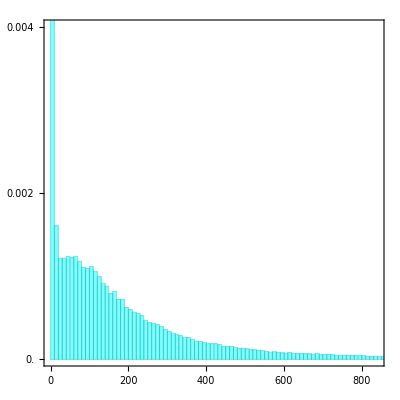

```mathematica
Histogram[Flatten[ctcfHiChipKb],{10},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0,840},{0,0.004}},FrameTicks->{{Range[0,0.007,0.002],None},(*left,right*){Range[0,800,200],None}        (*bottom,top*)}]
```

## Загрузка данных CTCF CHIA-PET

```mathematica
rawData=Import["C:\\петли\\ЭКСПЕРИМЕНТЫ\\данные для гистограмм\\CTCF_CHIA_PET_ALL.csv","Data"]
```

$Aborted

```mathematica
header=First[rawData];
rows=Rest[rawData];

(*Номера нужных столбцов определяются по названиям*)
cellLineColumn=First@FirstPosition[header,"cell_line"];
lengthColumn=First@FirstPosition[header,"loop_length_kb"];

(*Преобразование значения в число,если оно импортировалось как строка*)
toNumber[x_]:=If[NumberQ[x],N[x],ToExpression[x]];

cellLines={"GM12878","HeLa","K562","MCF7"};

(*Таблицы имеют вид {{длина1},{длина2},...}*)
lengthTables=AssociationMap[Function[cellLine,({toNumber[#[[lengthColumn]]]}&)/@Select[rows,#[[cellLineColumn]]==cellLine&]],cellLines];

(*Четыре отдельные таблицы*)
gm12878LoopLengths=lengthTables["GM12878"];
helaLoopLengths=lengthTables["HeLa"];
k562LoopLengths=lengthTables["K562"];
mcf7LoopLengths=lengthTables["MCF7"];
```

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\gm12878LoopLengthsCTCF.csv",gm12878LoopLengths]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\gm12878LoopLengthsCTCF.csv

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\helaLoopLengthsCTCF.csv",helaLoopLengths]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\helaLoopLengthsCTCF.csv

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\k562LoopLengthsCTCF.csv",k562LoopLengths]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\k562LoopLengthsCTCF.csv

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\mcf7LoopLengthsCTCF.csv",mcf7LoopLengths]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\mcf7LoopLengthsCTCF.csv

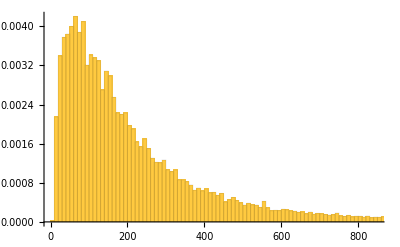

```mathematica
Histogram[Flatten[gm12878LoopLengths],15000,"PDF"]
```

```mathematica
{edges,counts}=HistogramList[Flatten[gm12878LoopLengths],15000,"PDF"];
gm12878LoopLengthsList=Transpose[{MovingAverage[edges,2],counts}];
{edges,counts}=HistogramList[Flatten[helaLoopLengths],15000,"PDF"];
helsLoopLengthsList=Transpose[{MovingAverage[edges,2],counts}];
{edges,counts}=HistogramList[Flatten[k562LoopLengths],15000,"PDF"];
k562LoopLengthsList=Transpose[{MovingAverage[edges,2],counts}];
{edges,counts}=HistogramList[Flatten[mcf7LoopLengths],15000,"PDF"];
mcf7LoopLengthsList=Transpose[{MovingAverage[edges,2],counts}];
```

```mathematica
gm12878LoopLengthsHist=SmoothKernelDistribution[Flatten[gm12878LoopLengths]];
```

```mathematica
helaLoopLengthsHist=SmoothKernelDistribution[Flatten[helaLoopLengths]];
```

```mathematica
k562LoopLengthsHist=SmoothKernelDistribution[Flatten[k562LoopLengths]];
```

```mathematica
mcf7LoopLengthsHist=SmoothKernelDistribution[Flatten[mcf7LoopLengths]];
```

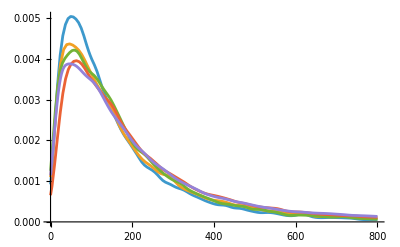

```mathematica
Plot[{PDF[mcf7LoopLengthsHist,x],PDF[helaLoopLengthsHist,x],PDF[k562LoopLengthsHist,x],PDF[gm12878LoopLengthsHist,x],PDF[ctcfHiChipK562Hist,x],PDF[K562rad21Hist,x],PDF[GMrad21Hist,x]},{x,0,800}]
```

```mathematica
ftRadK562= FindFit[K562rad21List,modelRad/.α->0/.γ->3/.γo->2/.lp->400,{{Ai,0.003}},{x}]
```

FindFit::fitd: The first argument K562rad21List in FindFit is not a list or a rectangular array.

FindFit[K562rad21List,-(Ai ⅇ^(-x/100) (-14112+3402 ⅇ^(-x/80)+9240 ⅇ^(-3 x/800)))/1470,{{Ai,0.003}},{x}]

```mathematica
Plot[modelRad/.α->0/.γ->3/.γo->2/.lp->400/.ftRadK562,{x,0,800}]
```

General::ivar: 0.0163429 is not a valid variable.

ReplaceAll::reps: {FindFit[K562rad21List,1.00069 Ai,{{Ai,0.003}},{0.0163429}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.3429 is not a valid variable.

ReplaceAll::reps: {FindFit[K562rad21List,1.52969 Ai,{{Ai,0.003}},{16.3429}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 32.6694 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[K562rad21List,1.80374 Ai,{{Ai,0.003}},{32.6694}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Show[Plot[modelRad/.α->0/.γ->3/.γo->2/.lp->400/.ftRadK562,{x,0,800}],ListPlot[K562rad21List]]
```

General::ivar: 0.0163429 is not a valid variable.

ReplaceAll::reps: {FindFit[K562rad21List,1.00069 Ai,{{Ai,0.003}},{0.0163429}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.3429 is not a valid variable.

ReplaceAll::reps: {FindFit[K562rad21List,1.52969 Ai,{{Ai,0.003}},{16.3429}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 32.6694 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[K562rad21List,1.80374 Ai,{{Ai,0.003}},{32.6694}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::lpn: K562rad21List is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[K562rad21List]].

Show[-Graphics-,ListPlot[K562rad21List]]

## Загрузка данных RAD21 CHIA-PET

```mathematica
ClearAll[importLoopLengthTable];
folder="C:\\петли\\ЭКСПЕРИМЕНТЫ\\данные для гистограмм\\rad21\\";

(*Находим PET-expanded файлы*)
files=Sort@FileNames["*_loop_lengths_pet_expanded.csv",folder];

(*Импорт одного файла:только колонка span_kb*)
importLoopLengthTable[file_]:=Module[{data,header,lengthColumn,values},data=Import[file,"CSV"];
header=First[data];
lengthColumn=First@FirstPosition[header,"span_kb"];
values=Rest[data][[All,lengthColumn]];
(*Одноколоночная таблица:{{длина1},{длина2},...}*)List/@N[values]];

(*Ассоциация:название файла->таблица длин*)
loopLengthTables=AssociationThread[FileBaseName/@files,importLoopLengthTable/@files];

(*Пять отдельных таблиц*)
{K562rep1,K562rep2,K562rep3,GMrep1,GMrep2}=Values[loopLengthTables];
```

```mathematica
rep1=N[HistogramList[Flatten[K562rep1],{10},"PDF"]][[2,1;;50]];
rep2=N[HistogramList[Flatten[K562rep2],{10},"PDF"]][[2,1;;50]];
rep3=N[HistogramList[Flatten[K562rep3],{10},"PDF"]][[2,1;;50]];
```

```mathematica
rep1=N[HistogramList[Flatten[GMrep1],{10},"PDF"]][[2,1;;50]];
rep2=N[HistogramList[Flatten[GMrep2],{10},"PDF"]][[2,1;;50]];
```

```mathematica
Mean[Mean[{Abs[rep1-rep2]}]]/Mean[Mean[{rep1,rep2}]]
```

0.145029

```mathematica
Mean[Mean[{Abs[rep1-rep2],Abs[rep1-rep3],Abs[rep2-rep3]}]]/Mean[Mean[{rep1,rep2,rep3}]]
```

0.157639

```mathematica
K562rep1[[1]]
```

{175.694}

```mathematica
Flatten[Join[K562rep1,K562rep2,K562rep3]]
```

```mathematica
K562rad21=Flatten[Join[K562rep1,K562rep2,K562rep3]];
GMrad21=Flatten[Join[GMrep1,GMrep2]];
```

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\K562rad21.csv",K562rad21]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\K562rad21.csv

```mathematica
Export["C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\GMrad21.csv",GMrad21]
```

C:\петли\ЭКСПЕРИМЕНТЫ\Обработка данны\new\GMrad21.csv

```mathematica
{edges,counts}=HistogramList[Flatten[K562rad21],15000,"PDF"];
K562rad21List=Transpose[{MovingAverage[edges,2],counts}];
```

```mathematica
{edges,counts}=HistogramList[Flatten[GMrad21],15000,"PDF"];
GMrad21List=Transpose[{MovingAverage[edges,2],counts}];
```

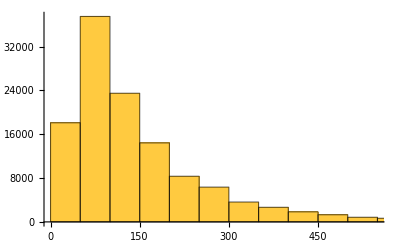

```mathematica
Histogram[Flatten[Join[K562rep1,K562rep2,K562rep3]],300]
```

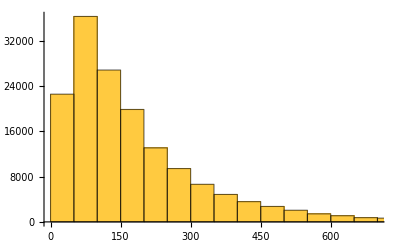

```mathematica
Histogram[Flatten[Join[GMrep1,GMrep2]],300]
```

```mathematica
K562rad21Hist=SmoothKernelDistribution[Flatten[K562rad21]];
```

```mathematica
GMrad21Hist=SmoothKernelDistribution[Flatten[GMrad21]];
```

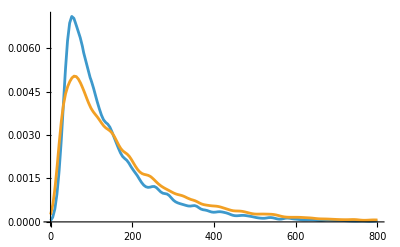

```mathematica
Plot[{PDF[K562rad21Hist,x],PDF[GMrad21Hist,x]},{x,0,800}]
```

```mathematica
tbls
```

tbls

```mathematica
criteria=<|"RadK562 + CTCFHi + CTCFK562"->(#[[12]]+#[[14]]+#[[15]]&),"RadGM + CTCFGM"->(#[[13]]+#[[16]]&),"CTCF HeLa"->(#[[17]]&),"CTCF MCF7"->(#[[18]]&)|>;

minimumResults=Function[criterion,Module[{values,minimum,positions},values=criterion/@tbls;
minimum=Min[values];
positions=Flatten@Position[values,minimum];
<|"Minimum"->minimum,"Positions"->positions,"Parameters"->{},"Rows"->tbls[[positions]]|>]]/@criteria;
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
ctcfHiChip=Table[If[ctcfHiChipKb[[i]]>=30,ctcfHiChipKb[[i]],Nothing],{i,1,Length[ctcfHiChipKb]}]
```

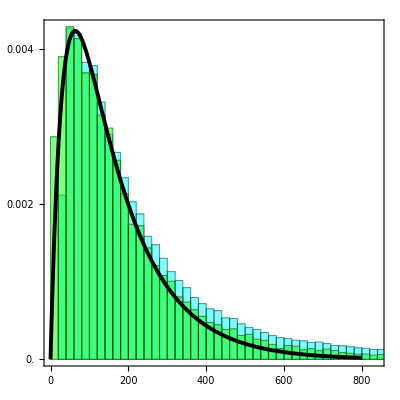

```mathematica
Show[Histogram[{Flatten[ctcfHiChip],Flatten[k562LoopLengths]},{20},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[0,1,0],Opacity[0.5]]},PlotRange->{{0,840},All},FrameTicks->{{Range[0,0.007,0.002],None},(*left,right*){Range[0,800,200],None}        (*bottom,top*)}],

Plot[{modelCTCF/.Ai->0.0165/.lp->400/.α->1.2/.γ->2.7/.γo->4/.x->xi},{xi,0,800},PlotStyle->{Directive[Black,Thickness[0.007]]}]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[k562LoopLengths].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[helaLoopLengths].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[gm12878LoopLengths].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

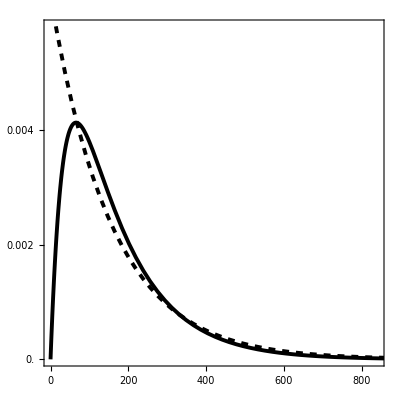

```mathematica
Show[Histogram[{Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths],Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths]},{20},"PDF",AspectRatio->1,PlotRange->{{0,840},{0,0.0058}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],
FrameTicks->{{Range[0,0.007,0.002],None},(*left,right*){Range[0,800,200],None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[1,1,0],Opacity[0.3]],Directive[RGBColor[0,0,1],Opacity[0.3]],Directive[RGBColor[1,0,0],Opacity[0.3]],Directive[RGBColor[0,1,0],Opacity[0]],Directive[RGBColor[0.5,0.5,1],Opacity[0]],Directive[RGBColor[1,0.5,0.5],Opacity[0]]}],Plot[{modelCTCF/.Ai->0.0167/.lp->431/.α->1.2/.γ->3.1/.γo->4/.x->xi,1/158*Exp[-xi/158]},{xi,0,900},PlotStyle->{Directive[Black,Thickness[0.007]],Directive[Black,Dashed,Thickness[0.007]]}]]
```

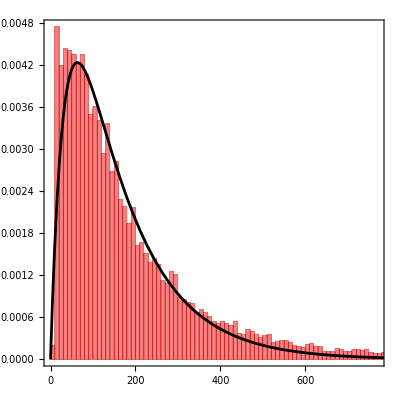

```mathematica
Show[Histogram[{Flatten[helaLoopLengths]},{10},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],Plot[{modelCTCF/.Ai->0.0165/.lp->400/.α->1.2/.γ->2.7/.γo->4/.x->xi},{xi,0,800},PlotStyle->{Directive[Black]}]]
```

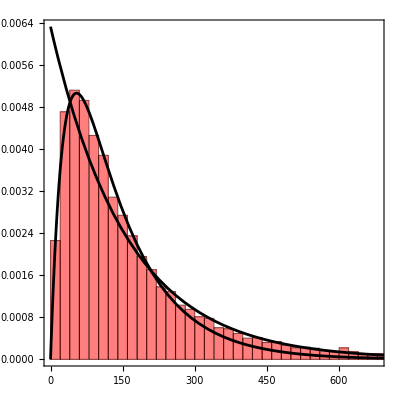

```mathematica
Show[Histogram[{Flatten[mcf7LoopLengths]},{20},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],Plot[{modelCTCF/.Ai->0.023/.lp->400/.α->1.2/.γ->4.4/.γo->4/.x->xi,1/158*Exp[-xi/158]},{xi,0,800},PlotStyle->{Directive[Black]}]]
```

```mathematica
FindFit[N[ctcfHiChipList],{modelCTCF/.lp->378/.α->1.2/.γ->2.6},{Ai,γ,γo},x]
```

{Ai→0.0198424,γ→1.,γo→3.54948}

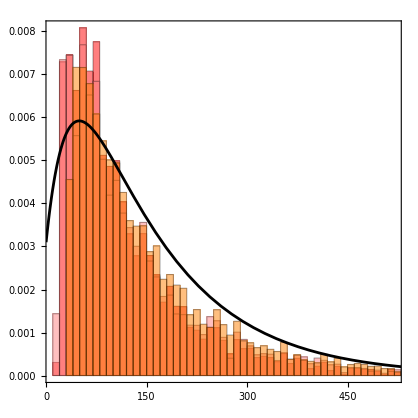

```mathematica
Show[Histogram[{Flatten[K562rep1],Flatten[K562rep2],Flatten[K562rep3]},{10},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[RGBColor[1,0.5,0.5],Opacity[1],EdgeForm[Black]],Directive[Pink,Opacity[1],EdgeForm[Black]],Directive[Orange,Opacity[0.5],EdgeForm[Black]]}],Plot[{modelRad/.Ai->0.0031/.lp->400/.α->1.2/.γ->2.7/.γo->4/.x->xi},{xi,0,800},PlotStyle->{Directive[Black]}]]
```

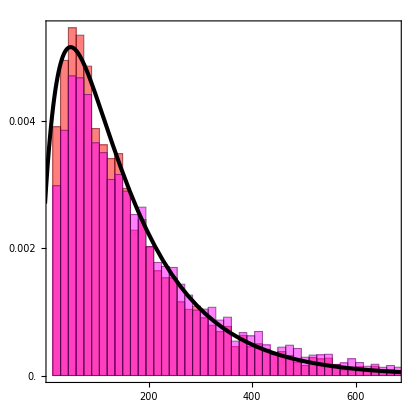

```mathematica
Show[Histogram[{Flatten[GMrep1],Flatten[GMrep2]},{15},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[RGBColor[1,0,0],Opacity[0.5],EdgeForm[Black]],Directive[RGBColor[1,0,1],Opacity[0.5],EdgeForm[Black]]},FrameTicks->{{Range[0,0.007,0.002],None},(*left,right*){Range[0,800,200],None}        (*bottom,top*)}],Plot[{modelRad/.Ai->0.0027/.lp->400/.α->1.2/.γ->2.7/.γo->4/.x->xi},{xi,0,800},PlotStyle->{Directive[Black,Thickness[0.007]]}]]
```

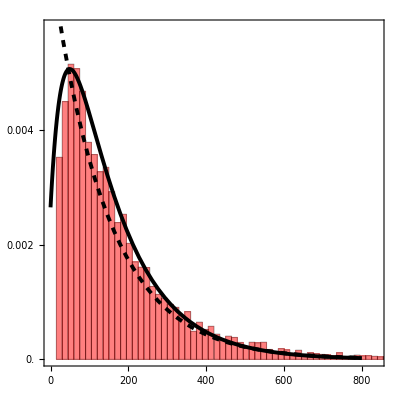

```mathematica
Show[Histogram[{GMrad21},{15},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[Red,Opacity[0.5],EdgeForm[Black]],Directive[Orange,Opacity[0.5],EdgeForm[Black]]},PlotRange->{{0,840},{0,0.0058}},FrameTicks->{{Range[0,0.007,0.002],None},(*left,right*){Range[0,800,200],None}        (*bottom,top*)}],Plot[{modelRad/.Ai->0.00265/.lp->400/.α->1.2/.γ->2.7/.γo->4/.x->xi,1/144*Exp[-xi/144]},{xi,0,800},PlotStyle->{Directive[Black,Thickness[0.007]],Directive[Black,Dashed,Thickness[0.007]]}]]
```

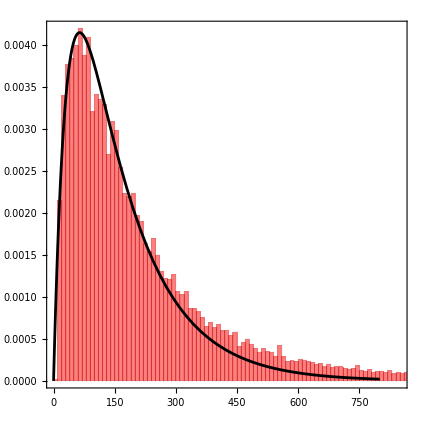

```mathematica
Show[Histogram[{Flatten[gm12878LoopLengths]},15000,"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16],ChartStyle->{Directive[Red,Opacity[0.5],EdgeForm[Black]]}],Plot[{modelCTCF/.Ai->0.016/.lp->400/.α->1.2/.γ->2.6/.γo->4/.x->xi},{xi,0,800},PlotStyle->{Directive[Black]}]]
```

```mathematica
NIntegrate[(PDF[gm12878LoopLengthsHist,x] - modelCTCF/.Ai->0.025/.lp->370/.α->0.7/.γ->2.6/.γo->2.3)^2,{x,0,800}]
```

0.0000160065

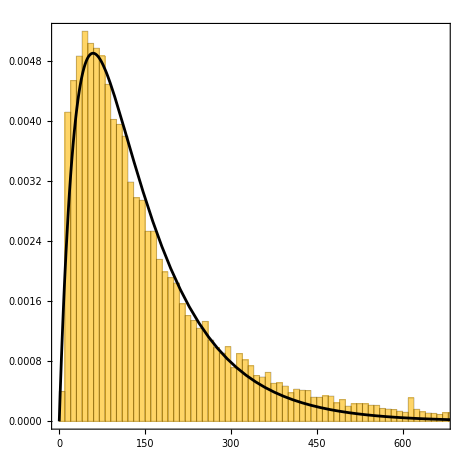

```mathematica
Show[Histogram[{Flatten[mcf7LoopLengths]},20000,"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16]],Plot[{modelCTCF/.Ai->0.032/.lp->350/.α->0.8/.γ->3.8/.γo->2.6/.x->xi},{xi,0,800},PlotStyle->{Directive[Black]}]]
```

```mathematica
Length[GMrad21 ]
```

155049

```mathematica
Length[ ]
```

```mathematica
NIntegrate[Abs[(PDF[mcf7LoopLengthsHist,x] -modelCTCF/.Ai->0.032/.lp->350/.α->0.8/.γ->3.8/.γo->2.6)],{x,0,800}]
```

0.110951

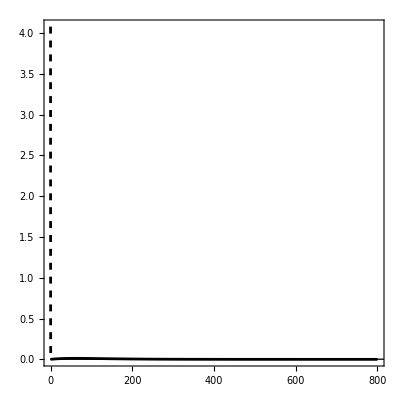

```mathematica
gr4e=Show[Histogram[{Flatten[k562LoopLengths],Flatten[ctcfHiChipKb]},5000,"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[16]],
(*Graphics[Text[Style["G1 (γ="<>ToString[γExp["Value"]]<>", γ_b="<>ToString[Round[γBExp["Value"]]]<>", γ_CTCF=1)",FontSize->16,FontFamily->"CMU Serif"],{0.06,2.35},{-1,0}]]*)
Plot[{modelCTCF/.Ai->0.015/.lp->400/.α->0./.γ->2.6/.γo->3.8/.x->xi},{xi,0,800},PlotStyle->{Directive[Black]}],Plot[{Am*Exp[-k*x*1000]/0.0028/.{Am->0.011421696614657459,k->0.009034414712030078}},{x,0,0.8},PlotStyle->{Directive[Black,Dashed]},PlotRange->All]]
```

```mathematica
criteria=<|"K562"->(#[[12]]+#[[14]]+#[[15]]&),"GM12878"->(#[[13]]+#[[16]]&),"HeLa"->(#[[17]]&),"MCF7"->(#[[18]]&)|>;
```

```mathematica
ClearAll[optimalAlphaSurface];

optimalAlphaSurface[data_,criterion_,lpValue_]:=Module[{selected,groups,bestRows},selected=Select[data,PossibleZeroQ[#[[1]]-lpValue]&];
groups=GatherBy[selected,#[[{2,3}]]&];
bestRows=First@MinimalBy[#,criterion]&/@groups;
(*{γ,γb,минимальный RMSE,оптимальный α}*){#[[2]],#[[3]],criterion[#],#[[4]]}&/@bestRows];
```

```mathematica
lpValue=First@DeleteDuplicates[tbls[[All,1]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

First::nofirst: Symbol[] has zero length and no first element.

```mathematica
rmsePlots=KeyValueMap[makeRMSEPlot,criteria];

GraphicsGrid[Partition[rmsePlots,2],Spacings->{0.5,0.5}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&].

GatherBy::list: List expected at position 1 in GatherBy[Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&],#1⟦{2,3}⟧&].

MinimalBy::arg1: The first argument is expected to be a list or association.

GatherBy::list: List expected at position 1 in GatherBy[Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&],#1⟦{2,3}⟧&].

Part::partw: Part 3 of Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&] does not exist.

Part::partw: Part 12 of Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&] does not exist.

Part::partw: Part 14 of Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[tbls,PossibleZeroQ[#1⟦1⟧-1. First[Symbol[]]]&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

ListContourPlot::arrayerr: {{{{{PossibleZeroQ[«1»]&}}}},{{{{Select[«2»]⟦3⟧}}}},{{{{Part[«2»]+Part[«2»]+Part[«2»]}}}},{{{{Select[«2»]⟦4⟧}}}}}⟦All,{1,2,3}⟧ must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[{{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}}}⟦All,{1,2,3}⟧,InterpolationOrder→1,PlotLegends→Automatic,Frame→True,FrameLabel→{γ,γb,RMSE},PlotLabel→K562,ColorFunction→TemperatureMap,PlotRange→All,ImageSize→400],minimumPoint$28295].

GatherBy::list: List expected at position 1 in GatherBy[Select[tbls,PossibleZeroQ[#1⟦1⟧-First[Symbol[]]]&],#1⟦{2,3}⟧&].

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

MinimalBy::arg1: The first argument is expected to be a list or association.

General::stop: Further output of MinimalBy::arg1 will be suppressed during this calculation.

ListContourPlot::arrayerr: {{{{{PossibleZeroQ[«1»]&}}}},{{{{Select[«2»]⟦3⟧}}}},{{{{Part[«2»]+Part[«2»]}}}},{{{{Select[«2»]⟦4⟧}}}}}⟦All,{1,2,3}⟧ must be a valid array.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[{{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}}}⟦All,{1,2,3}⟧,InterpolationOrder→1,PlotLegends→Automatic,Frame→True,FrameLabel→{γ,γb,RMSE},PlotLabel→GM12878,ColorFunction→TemperatureMap,PlotRange→All,ImageSize→400],minimumPoint$28433].

ListContourPlot::arrayerr: {{{{{PossibleZeroQ[«1»]&}}}},{{{{Select[«2»]⟦3⟧}}}},{{{{Select[«2»]⟦17⟧}}}},{{{{Select[«2»]⟦4⟧}}}}}⟦All,{1,2,3}⟧ must be a valid array.

General::stop: Further output of ListContourPlot::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListContourPlot[{{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}},{{{{«1»}}}}}⟦All,{1,2,3}⟧,InterpolationOrder→1,PlotLegends→Automatic,Frame→True,FrameLabel→{γ,γb,RMSE},PlotLabel→HeLa,ColorFunction→TemperatureMap,PlotRange→All,ImageSize→400],minimumPoint$28489].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

-Graphics-

```mathematica
data=Import["C:\\Users\\kitte\\Downloads\\GM12878_CTCF_GSM1872886_loop_lengths_pet_expanded.csv\\GM12878_CTCF_GSM1872886_loop_lengths_pet_expanded.csv","Data"]
```

# Unified fitting of ChIA-PET and HiChIP loop-length distributions

```mathematica
(* modelRad and modelCTCF must be defined before this code is run.
   Expected model symbols: x, Ai, α, γ, γo, lp. *)

(* ------------------------------------------------------------------ *)
(* 1. Input files and dataset settings                                 *)
(* ------------------------------------------------------------------ *)

baseDir = NotebookDirectory[];

(* Output directory of chia_pet_unified_pipeline_no_pet_filter.py *)
chiaPetDir = "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\chia_pet_results\\loop_length";

(* The separate HiChIP table *)
hiChipFile = FileNameJoin[{baseDir, "hichip_results", "CTCF_HICHIP.csv"}];

binKb = 10.;

ClearAll[findOne];

findOne::files = "Pattern `1` matched `2` files: `3`.";

findOne[directory_, pattern_] := Module[
  {files = FileNames[pattern, directory]},

  If[Length[files] != 1,
    Message[findOne::files, pattern, Length[files], files];
    Abort[]
  ];

  First[files]
];

(* These are the six combined PET-expanded files generated by Python.
   The *.csv* suffix accepts both .csv and .csv.gz. *)
chiaPetFiles = <|
  "RadK562" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\K562rad21.csv",

  "RadGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\GMrad21.csv",

  "CTCFK562" -> "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\k562LoopLengthsCTCF.csv",

  "CTCFGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\gm12878LoopLengthsCTCF.csv",

  "CTCFHeLa" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\helaLoopLengthsCTCF.csv",

  "CTCFMCF7" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\mcf7LoopLengthsCTCF.csv"
|>;

If[!FileExistsQ[hiChipFile],
  Print["HiChIP file was not found: ", hiChipFile];
  Abort[]
];

(* The order is intentional:
   columns 5-11  = fitted amplitudes;
   columns 12-18 = RMSE, matching the previous tbls structure;
   columns 19-25 = nRMSE. *)
datasetOrder = {
  "RadK562",
  "RadGM",
  "CTCFK562Hi",
  "CTCFK562",
  "CTCFGM",
  "CTCFHeLa",
  "CTCFMCF7"
};

specs = <|
  "RadK562" -> <|
    "File" -> chiaPetFiles["RadK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30.,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "RadGM" -> <|
    "File" -> chiaPetFiles["RadGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "CTCFK562Hi" -> <|
    "File" -> hiChipFile,
    "Column" -> "interaction_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 30.,              (* remove HiChIP short-range contacts *)
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,       (* lp grid is in kb; model uses Mb *)
    "A0" -> 3.
  |>,

  "CTCFK562" -> <|
    "File" -> chiaPetFiles["CTCFK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFGM" -> <|
    "File" -> chiaPetFiles["CTCFGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFHeLa" -> <|
    "File" -> chiaPetFiles["CTCFHeLa"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFMCF7" -> <|
    "File" -> chiaPetFiles["CTCFMCF7"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>
|>;
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 2. Import and construction of uniformly binned PDFs                 *)
(* ------------------------------------------------------------------ *)

ClearAll[importCSV, toNumber, readNumericColumn, makePDFData];

(* Import works directly for ordinary CSV. For .csv.gz, Mathematica usually
   detects compression automatically; the fallback explicitly decompresses
   the file and parses the resulting CSV string. *)
importCSV[file_] := Quiet @ Check[
  Import[file, "CSV"],
  ImportString[Import[file, "String"], "CSV"]
];

toNumber[value_] := Quiet @ Check[
  N @ If[NumberQ[value], value, ToExpression @ ToString[value]],
  Missing["NotNumeric"]
];

readNumericColumn[file_, column_] := Module[
  {table, header, position, values},

  table = importCSV[file];
  header = First[table];
  position = FirstPosition[header, column, Missing["NotFound"]];

  If[MissingQ[position],
    Print["Column \"", column, "\" was not found in ", file];
    Abort[]
  ];

  values = toNumber /@ Rest[table][[All, First[position]]];
  Select[DeleteMissing[values], NumericQ]
];

makePDFData[spec_] := Module[
  {values, edges, density, scale},

  values = readNumericColumn[spec["File"], spec["Column"]];

  (* Filtering is performed before HistogramList, so the retained
     distribution is normalized again. For HiChIP this removes <30 kb. *)
  values = Select[
    values,
    spec["MinKb"] <= # <= spec["MaxKb"] &
  ];

  If[values === {},
    Print["No observations remain for ", spec["File"]];
    Abort[]
  ];

  {edges, density} = HistogramList[
    values,
    {spec["MinKb"], spec["MaxKb"], binKb},
    "PDF"
  ];

  scale = spec["XScale"];

  (* If x is converted from kb to Mb, density is converted from
     probability/kb to probability/Mb to preserve unit integral. *)
  Transpose[{
    MovingAverage[edges, 2] scale,
    density/scale
  }]
];

fitData = AssociationMap[makePDFData[specs[#]] &, datasetOrder];
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 3. Fit one dataset at one parameter-grid point                      *)
(* ------------------------------------------------------------------ *)

ClearAll[fitOne];

fitOne[name_, {lpValue_, gammaValue_, gamma0Value_, alphaValue_}] :=
 Module[
  {spec, data, model, fit, observed, predicted, rmse, nrmse},

  spec = specs[name];
  data = fitData[name];

  model = spec["Model"] /. {
      α -> alphaValue,
      γ -> gammaValue,
      γo -> gamma0Value,
      lp -> lpValue spec["LpScale"]
    };

  fit = Quiet @ Check[
    FindFit[data, model, {{Ai, spec["A0"]}}, x],
    $Failed
  ];

  If[fit === $Failed,
    Return[{Indeterminate, Infinity, Infinity}]
  ];

  observed = data[[All, 2]];
  predicted = N[(model /. fit /. x -> #)] & /@ data[[All, 1]];

  rmse =  Mean[Abs[(observed - predicted)]];
  nrmse = rmse/Mean[observed];

  {Ai /. fit, rmse, nrmse}
];
```

```mathematica
datasetOrder
```

{RadK562,RadGM,CTCFK562Hi,CTCFK562,CTCFGM,CTCFHeLa,CTCFMCF7}

```mathematica
(* ------------------------------------------------------------------ *)
(* 4. Parameter grid and complete fit table                            *)
(* ------------------------------------------------------------------ *)

lpGrid = Range[431, 431, 50];
gammaGrid = N @ Range[0.1, 10, 0.3];
gamma0Grid =N @ Range[0.1, 10, 0.3];
alphaGrid = N @ Range[1.2,1.2, 0.2];

parameterGrid = Tuples[{
  lpGrid,
  gammaGrid,
  gamma0Grid,
  alphaGrid
}];

ClearAll[fitRow];

fitRow[parameters_] := Module[{results},
  results = fitOne[#, parameters] & /@ datasetOrder;

  Join[
    parameters,
    results[[All, 1]],     (* amplitudes *)
    results[[All, 2]],     (* RMSE *)
    results[[All, 3]]      (* nRMSE *)
  ]
];

progress = 0;

tbls = Monitor[
  Map[
    Function[parameters,
      progress++;
      fitRow[parameters]
    ],
    parameterGrid
  ],
  Row[{"Fitted parameter sets: ", progress, "/", Length[parameterGrid]}]
]
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 5. Column names and export                                          *)
(* ------------------------------------------------------------------ *)

Export[
  FileNameJoin[{baseDir, "all_loop_distribution_fits.csv"}],  "CSV"
];
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 6. Useful views                                                     *)
(* ------------------------------------------------------------------ *)

(* Previous RMSE indices remain unchanged:
   12,19 RadK562
   13,20 RadGM
   14,21 CTCFK562Hi
   15,22 CTCFK562
   16,23 CTCFGM
   17,24 CTCFHeLa
   18,25 CTCFMCF7

   nRMSE values occupy columns 19-25 in the same order. *)

(* Example: inspect the prepared HiChIP distribution.
   Its first x value should be close to 0.035 Mb for 10-kb bins. *)
fitData["CTCFK562Hi"] // Take[#, UpTo[5]] &
```

{{35.,0.00452333},{45.,0.00458964},{55.,0.00452957},{65.,0.00460368},{75.,0.00437666}}

```mathematica
tblsHeLa=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,24]])},{i,1,Length[tbls]}];
```

```mathematica
gammaC=Around[3.1,0.8](*gamma of cohesins + dynamic correction*);
gammaB=Around[1.8,0.6];
```

```mathematica
levelsHela=Range[Min[tblsHeLa[[All,3]]],0.8,0.03];
zrangeHela={Min[levelsHela],Max[levelsHela]};
```

```mathematica
legendHela=ContourPlot[y,{γ,0,2},{y,zrangeHela[[1]],zrangeHela[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsHela,ContourShading->True,PlotRange->zrangeHela,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,0,1,0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gHela=Show[ListContourPlot[tblsHeLa,Frame->True,PlotRange->{zrangeHela[[1]],zrangeHela[[2]]},Contours->levelsHela,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

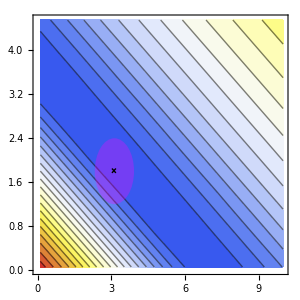

```mathematica
GraphicsRow[{gHela,legendHela}]
```

```mathematica
tblsGM=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,20]]+tbls[[i,23]])/2},{i,1,Length[tbls]}];
```

```mathematica
levelsGM=Range[Min[tblsGM[[All,3]]],0.8,0.03];
zrangeGM={Min[levelsGM],Max[levelsGM]};
```

```mathematica
zrangeGM[[2]]
```

0.777922

```mathematica
legendGM=ContourPlot[y,{γ,0,2},{y,zrangeGM[[1]],zrangeGM[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsGM,ContourShading->True,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,Round[zrangeGM[[1]],0.1],zrangeGM[[2]],0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gGM=Show[ListContourPlot[tblsGM,Frame->True,PlotRange->{zrangeGM[[1]],zrangeGM[[2]]},Contours->levelsGM,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

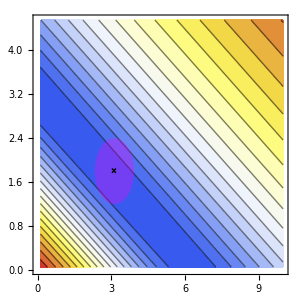

```mathematica
GraphicsRow[{gGM,legendGM}]
```

```mathematica
tblsK562=Table[{tbls[[i,2]],tbls[[i,3]]/(1+1.2),(tbls[[i,21]]+tbls[[i,22]])/2},{i,1,Length[tbls]}];
```

```mathematica
levelsK562=Range[Min[tblsK562[[All,3]]],0.8,0.03];
zrangeK562={Min[levelsK562],Max[levelsK562]};
```

```mathematica
zrangeK562
```

{0.0936284,0.783628}

```mathematica
legendK562=ContourPlot[y,{γ,0,2},{y,zrangeK562[[1]],zrangeK562[[2]]},FrameLabel->{None,None,None,None},
FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],AxesOrigin->{0,0},Frame->True,AspectRatio->20,Contours->levelsK562,ContourShading->True,PlotLegends->None,ColorFunction->"TemperatureMap",ColorFunctionScaling->True,FrameTicks->{{None,Table[{γ,γ},{γ,0,1,0.1}]},{None,None}},FrameTicksStyle->Directive[14,FontFamily->"CMU Serif",Black],ImageSize->45.5,PlotRangePadding->None];
```

```mathematica
gK562=Show[ListContourPlot[tblsK562,Frame->True,PlotRange->{zrangeK562[[1]],zrangeK562[[2]]},Contours->levelsGM,FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],ColorFunction->"TemperatureMap"],Graphics[{RGBColor[1,0,1],Opacity[0.3],Disk[{gammaC["Value"],gammaB["Value"]},{gammaC["Error"],gammaB["Error"]}]}],Graphics[Line[{{{gammaC["Value"]-0.08,gammaB["Value"]-0.04},{gammaC["Value"]+0.08,gammaB["Value"]+0.04}},{{gammaC["Value"]-0.08,gammaB["Value"]+0.04},{gammaC["Value"]+0.08,gammaB["Value"]-0.04}}}]],ImageSize->300];
```

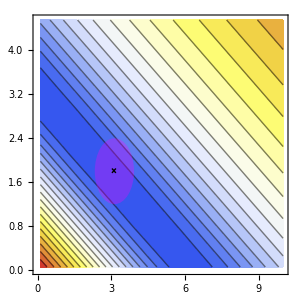

```mathematica
GraphicsRow[{gK562,legendK562}]
```

```mathematica
GraphicsRow[{gHela,legendHela,gGM,legendGM,gK562,legendK562}]
```

Table::iterb: Iterator {γ,Round[Range[∞,0.8,0.03],0.1],Range[∞,0.8,0.03],0.1} does not have appropriate bounds.

Range::range: Range specification in Range[∞,0.8,0.03] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,«15»,Method,PlotInteractivity,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,«15»,Method,PlotInteractivity,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}],{«1»}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

Median::rectn: A rectangular array of real numbers is expected at position 1 in Median[{1.,20.,1.,20.,Lookup[System`Dump`opts,System`Dump`name],20.}].

Median::rectn: A rectangular array of real numbers is expected at position 1 in Median[{System`Dump`opts}].

Part::partd: Part specification {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,1⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

Part::partd: Part specification {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,2⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,2⟧ is not a valid Association or a list.

Part::partd: Part specification {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DeleteMissing::invrp: The argument {{{{26.001,7.16378},{27.5371,6.43185}},{{0.5,21.8896},{1.5,9.15332}},{{26.001,7.16378},{27.5371,6.43185}},{{0.5,1.5},{1.5,0.5}},Lookup[System`Dump`opts,System`Dump`name],{{0.5,21.8896},{1.5,9.15332}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

General::stop: Further output of DeleteMissing::invrp will be suppressed during this calculation.

-Graphics-